# :d83d:dce1 Bset 3: The power of LTI

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## 3-1-3 rotations

```mathematica
RotationMatrix[ϕ,{0,0,1}]//MatrixForm
```

(Cos[ϕ] | -Sin[ϕ] | 0
Sin[ϕ] | Cos[ϕ] | 0
0 | 0 | 1)

```mathematica
ψ
```

```mathematica
ψ
```

## Projectile Simulation

```mathematica
With[{context="sim`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
initialConditions={x[0]=={0,0},x'[0]=={2,50}}
forces=<|fg->{0,-m g}|>
params=<|m->5,g->9.8|>


de={(fg==m x''[t])}/.forces/.params
```

{x[0]=={0,0},x'[0]=={2,50}}

<|fg→{0,-g m}|>

<|m→5,g→9.8|>

{{0,-49.}==5 x''[t]}

InterpolatingFunction[{{0., 10.}}, <>][t]

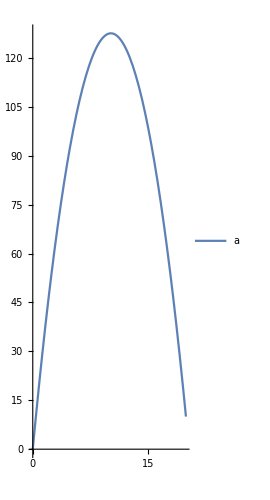

```mathematica
sol=NDSolveValue[Join[initialConditions,de],x[t],{t,0,10}]
ParametricPlot[sol/.t->x,{x,0,10},PlotLegends->{"a","b"}]
```

```mathematica
sol/.t->5
```

{50.,0.5}

```mathematica
With[{context="sim`"},If[Context[]==context,End[],"Not in context"]]
```